# Interpolation Coefficients

```mathematica
RepK={ki->λ^i,kim->λ^i/λ,kip->λ^i λ};
AssumSimply={λ>1,ni>0,nim>0};
```

## Exponential shape

```mathematica
Logn[k_]=Log[Cc] -β k;
SolExp=Solve[{Log[ni]==Logn[ki],Log[nim]==Logn[kim]},{β,Cc}]//Simplify
```

{{β→ConditionalExpression[(-Log[ni]+Log[nim])/(ki-kim), -π≤Im[(kim Log[ni]-ki Log[nim])/(ki-kim)]<π],Cc→ConditionalExpression[ⅇ^((-kim Log[ni]+ki Log[nim])/(ki-kim)), -π≤Im[(kim Log[ni]-ki Log[nim])/(ki-kim)]<π]}}

```mathematica
SolExpSymp=FullSimplify[SolExp/.RepK,AssumSimply][[1]]
```

{β→(λ^(1-i) Log[nim/ni])/(-1+λ),Cc→ni^(1/(1-λ)) nim^(λ/(-1+λ))}

## Linear integration for signed fields

Linear extrapolation to k=0

```mathematica
nk[k_]=a +b k;
SolLin=Solve[{nk[k1]==n1,nk[k2]==n2},{a,b}][[1]]
Integrate[nk[k]/.SolLin,{k,0,k1}]//FullSimplify
```

{a→-(k2 n1-k1 n2)/(k1-k2),b→-(-n1+n2)/(k1-k2)}

(k1 (-2 k2 n1+k1 (n1+n2)))/(2 (k1-k2))

```mathematica
`
```

## Power-law and exponential

```mathematica
DD=Det[{{1,-km,-Log[km]},{1,-k,-Log[k]},{1,-kp,-Log[kp]}}]
```

km Log[k]-kp Log[k]-k Log[km]+kp Log[km]+k Log[kp]-km Log[kp]

```mathematica
DDλ=FullSimplify[DD/.{k->λ^î,km->λ^(î-1),kp->λ^(î+1)},{λ>1,i>0}]
```

(-1+λ) λ^(-1+î) (λ Log[λ^(-1+î)]-(1+λ) Log[λ^î]+Log[λ^(1+î)])

```mathematica
FullSimplify[Inverse[{{1,-km,-Log[km]},{1,-k,-Log[k]},{1,-kp,-Log[kp]}}]/.{k->λ^î,km->λ^(î-1),kp->λ^(î+1)},{λ>1,i>0}]
```

{{-(λ (λ Log[λ^î]-Log[λ^(1+î)]))/((-1+λ) (λ Log[λ^(-1+î)]-(1+λ) Log[λ^î]+Log[λ^(1+î)])),(λ^2 Log[λ^(-1+î)]-Log[λ^(1+î)])/((-1+λ) (λ Log[λ^(-1+î)]-(1+λ) Log[λ^î]+Log[λ^(1+î)])),(-λ Log[λ^(-1+î)]+Log[λ^î])/((-1+λ) (λ Log[λ^(-1+î)]-(1+λ) Log[λ^î]+Log[λ^(1+î)]))},{-(λ^(1-î) (Log[λ^î]-Log[λ^(1+î)]))/((-1+λ) (λ Log[λ^(-1+î)]-(1+λ) Log[λ^î]+Log[λ^(1+î)])),(λ^(1-î) (Log[λ^(-1+î)]-Log[λ^(1+î)]))/((-1+λ) (λ Log[λ^(-1+î)]-(1+λ) Log[λ^î]+Log[λ^(1+î)])),(λ^(1-î) (-Log[λ^(-1+î)]+Log[λ^î]))/((-1+λ) (λ Log[λ^(-1+î)]-(1+λ) Log[λ^î]+Log[λ^(1+î)]))},{-λ/(λ Log[λ^(-1+î)]-(1+λ) Log[λ^î]+Log[λ^(1+î)]),(1+λ)/(λ Log[λ^(-1+î)]-(1+λ) Log[λ^î]+Log[λ^(1+î)]),-1/(λ Log[λ^(-1+î)]-(1+λ) Log[λ^î]+Log[λ^(1+î)])}}

```mathematica
MI=Simplify[Inverse[{{1,-λ^(i-1),-(i-1)Log[λ]},{1,-λ^i,-i Log[λ]},{1,-λ^(i+1),-(i+1)Log[λ]}}],λ>1]
```

{{((-1+i (-1+λ)) λ)/(-1+λ)^2,(1+i+λ^2-i λ^2)/(-1+λ)^2,(i (-1+λ)-λ)/(-1+λ)^2},{-λ^(1-i)/(-1+λ)^2,(2 λ^(1-i))/(-1+λ)^2,-λ^(1-i)/(-1+λ)^2},{λ/((-1+λ) Log[λ]),(1+λ)/(Log[λ]-λ Log[λ]),1/((-1+λ) Log[λ])}}

```mathematica
Sol=Simplify[MI.{Lognim,Logni,Lognip},λ>1]
```

{(-((Lognim+Lognip) λ)+i (-1+λ) (Lognip+Lognim λ)+Logni (1+i+λ^2-i λ^2))/(-1+λ)^2,((2 Logni-Lognim-Lognip) λ^(1-i))/(-1+λ)^2,(Lognip+Lognim λ-Logni (1+λ))/((-1+λ) Log[λ])}

```mathematica
Integrate[Cc k^(-α)Exp[-β k],k]
```

-(Cc k^-α (k β)^α Gamma[1-α,k β])/β

```mathematica
Simplify[-(Cc k^-α (k β)^α Gamma[1-α,k β])/β,k>0]
```

-Cc β^(-1+α) Gamma[1-α,k β]

```mathematica
Limit[β^(-1+α) Gamma[1-α,k β],α->0]
```

ⅇ^(-k β)/β

```mathematica
dif=D[(β^(-1+α) Gamma[1-α,k β]-ⅇ^(-k β)/β),k]
```

ⅇ^(-k β)-ⅇ^(-k β) β^α (k β)^-α

```mathematica
Plot[Abs[]/.{α->.0001,β->1/10},{k,0,100},PlotRange->All]
```

General::ivar: 0.00204286 is not a valid variable.

General::ivar: 2.04286 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

(ⅇ^(-k/10) k^2)/(1+k^3)

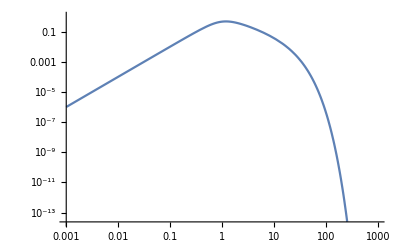

```mathematica
n[k_]=k^2 Exp[-k/10]/(1+k^3)
LogLogPlot[n[k],{k,1/1000,1000}]
```

```mathematica
λp=2.^(.25);
ip=50;
λp ^ip

Sol/.{Lognim->Log[n[λp^(ip-1)]],Logni->Log[n[λp^(ip)]],Lognip->Log[n[λp^(ip+1)]],i->ip,λ->λp}
```

5792.62

{-6.09728×10^-10,0.1,1.}

```mathematica
{-((Lognim+Lognip) λ)+i (-1+λ) (Lognip+Lognim λ)+Logni (1+i+λ^2-i λ^2),(2 Logni-Lognim-Lognip) λ^(1-i),((Lognip+Lognim λ-Logni (1+λ))(-1+λ))/((-1+λ) Log[λ])}
```

{-((Lognim+Lognip) λ)+i (-1+λ) (Lognip+Lognim λ)+Logni (1+i+λ^2-i λ^2),(2 Logni-Lognim-Lognip) λ^(1-i),(Lognip+Lognim λ-Logni (1+λ))/Log[λ]}

## Quadratic interpolation

```mathematica
fim[x_]=(xi -x)(xip-x)/((xi-xim)(xip-xim))fim
fi[x_]=(xim -x)(xip-x)/((xim-xi)(xip-xi))fi
fip[x_]=(xim -x)(xi-x)/((xim-xip)(xi-xip))fip
f[x_]=fim[x]+fi[x]+fip[x]
```

(fim (-x+xi) (-x+xip))/((xi-xim) (-xim+xip))

(fi (-x+xim) (-x+xip))/((-xi+xim) (-xi+xip))

(fip (-x+xi) (-x+xim))/((xi-xip) (xim-xip))

(fip (-x+xi) (-x+xim))/((xi-xip) (xim-xip))+(fi (-x+xim) (-x+xip))/((-xi+xim) (-xi+xip))+(fim (-x+xi) (-x+xip))/((xi-xim) (-xim+xip))

```mathematica
Integrate[fim[x],{x,xim,xi}]//Simplify
Integrate[fi[x],{x,xim,xi}]//Simplify
Integrate[fip[x],{x,xim,xi}]//Simplify

Integrate[fim[x],{x,xim,xi}]/.{xim-> a + i-1,xi-> a + i,xip-> a + i+1}//Simplify
Integrate[fi[x],{x,xim,xi}]/.{xim-> a + i-1,xi-> a + i,xip-> a + i+1}//Simplify
Integrate[fip[x],{x,xim,xi}]/.{xim-> a + i-1,xi-> a + i,xip-> a + i+1}//Simplify
```

(fim (xi-xim) (xi+2 xim-3 xip))/(6 (xim-xip))

(fi (xi-xim) (2 xi+xim-3 xip))/(6 (xi-xip))

(fip (xi-xim)^3)/(6 (xi-xip) (-xim+xip))

(5 fim)/12

(2 fi)/3

-fip/12